Integral[f[p,u],{p,0,1}] can be expressed analytically as a function of u and is given in the definition “fanalytic”.
But, it is too difficult for symbolic algebra systems such as Mathematica (actually it did it!)
The result is a linear combination of a known set of basis functions (known by theoretical arguments which
use the singularity and branch cut structure of the integral).
So, we could do the integral numerically at a set of values for u, then fit the result.
This can be done by standard fits at some level of precision.
The question is, can we do it at a high enough precision to find the exact coefficients.
Note that they are simple rational numbers times (known) powers of pi and zeta[3].
In another notebook we will show how to fit high precision numerical results to exact expressions.

```mathematica
f[p_,u_] :=(-(1/(24 π^2 (p+u-p u)^2)) (p π^2-2 p π^2 u+π^2 u^2+p π^2 u^2-3 (p (-1+u)^2+u^2) Log[p]^2-24 u Log[(1-u) u]-24 p u Log[(1-u) u]+24 u^2 Log[(1-u) u]+24 p u^2 Log[(1-u) u]-12 p Log[(1-u) u]^2+24 p u Log[(1-u) u]^2-12 u^2 Log[(1-u) u]^2-12 p u^2 Log[(1-u) u]^2+12 Log[p] ((-1-p) (-1+u) u+(p (-1+u)^2+u^2) Log[(1-u) u])-12 (p (-1+u)^2+u^2) PolyLog[2,p])-(1/(24 π^2)) (π^2 (1-2 u+2 u^2)+12 (1-2 u+2 u^2) Log[1-u]^2-48 (-1+u) u Log[u]+12 (1-2 u+2 u^2) Log[u]^2+24 Log[1-u] (-2 (-1+u) u+(1-2 u+2 u^2) Log[u]))) 1/(1-p)
```

```mathematica
fanalytic = Expand[((4-12 u+8 u^2+4 I π (1-3 u+2 u^2)+π^2 (1-2 u+2 u^2)) Log[-1+u])/(4 π^2)+((-2+6 u-4 u^2+I π (1-2 u+2 u^2)) Log[-1+u]^2)/(4 π^2)-((1-2 u+2 u^2) Log[-1+u]^3)/(12 π^2)+((4 I π+4 (1-2 u)^2+π^2 (3-6 u+6 u^2)) Log[u])/(8 π^2)+(I (I+π-2 π u+2 π u^2) Log[-1+u] Log[u])/(2 π^2)-((1-2 u+2 u^2) Log[-1+u]^2 Log[u])/(4 π^2)+((u (-3+2 u)+2 I π (1-2 u+2 u^2)) Log[u]^2)/(2 π^2)+((-1+2 u-2 u^2) Log[-1+u] Log[u]^2)/π^2-((1-2 u+2 u^2) Log[u]^3)/(2 π^2)+((1-2 u) PolyLog[2,1-u])/(2 π^2)+((1-6 u+4 u^2+2 I π (1-2 u+2 u^2)) PolyLog[2,(-1+u)/u])/(4 π^2)-((1-2 u+2 u^2) Log[-1+u] PolyLog[2,(-1+u)/u])/(2 π^2)-((1-2 u+2 u^2) Log[u] PolyLog[2,(-1+u)/u])/(2 π^2)+((1-2 u+2 u^2) Log[u] PolyLog[2,u])/(2 π^2)-((1-2 u+2 u^2) PolyLog[3,(-1+u)/u])/(4 π^2)-((1-2 u+2 u^2) PolyLog[3,u])/(2 π^2)+((1-2 u+2 u^2) PolyLog[3,u/(-1+u)])/(2 π^2)+1/(24 π^2) (-24 I π (1-3 u+2 u^2)-2 I π^3 (1-2 u+2 u^2)+π^2 (11-29 u+18 u^2)-6 (1-2 u+2 u^2) Zeta[3])];
analytic = N[fanalytic]
```

(0.427885-0.580109 ⅈ)-(1.14744-1.47853 ⅈ) u+(0.689103-1.16022 ⅈ) u^2+(0.351321+0.31831 ⅈ) Log[-1.+u]-(0.803964+0.95493 ⅈ) u Log[-1.+u]+(0.702642+0.63662 ⅈ) u^2 Log[-1.+u]-(0.0506606-0.0795775 ⅈ) Log[-1.+u]^2+(0.151982-0.159155 ⅈ) u Log[-1.+u]^2-(0.101321-0.159155 ⅈ) u^2 Log[-1.+u]^2-0.00844343 Log[-1.+u]^3+0.0168869 u Log[-1.+u]^3-0.0168869 u^2 Log[-1.+u]^3+(0.425661+0.159155 ⅈ) Log[u]-0.952642 u Log[u]+0.952642 u^2 Log[u]-(0.0506606-0.159155 ⅈ) Log[-1.+u] Log[u]-(0.+0.31831 ⅈ) u Log[-1.+u] Log[u]+(0.+0.31831 ⅈ) u^2 Log[-1.+u] Log[u]-0.0253303 Log[-1.+u]^2 Log[u]+0.0506606 u Log[-1.+u]^2 Log[u]-0.0506606 u^2 Log[-1.+u]^2 Log[u]+(0.+0.31831 ⅈ) Log[u]^2-(0.151982+0.63662 ⅈ) u Log[u]^2+(0.101321+0.63662 ⅈ) u^2 Log[u]^2-0.101321 Log[-1.+u] Log[u]^2+0.202642 u Log[-1.+u] Log[u]^2-0.202642 u^2 Log[-1.+u] Log[u]^2-0.0506606 Log[u]^3+0.101321 u Log[u]^3-0.101321 u^2 Log[u]^3+0.0506606 PolyLog[2.,1.-1. u]-0.101321 u PolyLog[2.,1.-1. u]+(0.0253303+0.159155 ⅈ) PolyLog[2.,(-1.+u)/u]-(0.151982+0.31831 ⅈ) u PolyLog[2.,(-1.+u)/u]+(0.101321+0.31831 ⅈ) u^2 PolyLog[2.,(-1.+u)/u]-0.0506606 Log[-1.+u] PolyLog[2.,(-1.+u)/u]+0.101321 u Log[-1.+u] PolyLog[2.,(-1.+u)/u]-0.101321 u^2 Log[-1.+u] PolyLog[2.,(-1.+u)/u]-0.0506606 Log[u] PolyLog[2.,(-1.+u)/u]+0.101321 u Log[u] PolyLog[2.,(-1.+u)/u]-0.101321 u^2 Log[u] PolyLog[2.,(-1.+u)/u]+0.0506606 Log[u] PolyLog[2.,u]-0.101321 u Log[u] PolyLog[2.,u]+0.101321 u^2 Log[u] PolyLog[2.,u]-0.0253303 PolyLog[3.,(-1.+u)/u]+0.0506606 u PolyLog[3.,(-1.+u)/u]-0.0506606 u^2 PolyLog[3.,(-1.+u)/u]-0.0506606 PolyLog[3.,u]+0.101321 u PolyLog[3.,u]-0.101321 u^2 PolyLog[3.,u]+0.0506606 PolyLog[3.,u/(-1.+u)]-0.101321 u PolyLog[3.,u/(-1.+u)]+0.101321 u^2 PolyLog[3.,u/(-1.+u)]

```mathematica
Integrate[f[p,u] ,{p,0,1},Assumptions->0<u<1]
```

-1/(24 π^2)(π^2-7 π^2 u+6 π^2 u^2-24 Log[1-u]+72 u Log[1-u]-48 u^2 Log[1-u]+12 Log[1-u]^2-36 u Log[1-u]^2+24 u^2 Log[1-u]^2+2 Log[1-u]^3-4 u Log[1-u]^3+4 u^2 Log[1-u]^3-12 Log[u]-3 π^2 Log[u]+48 u Log[u]+6 π^2 u Log[u]-48 u^2 Log[u]-6 π^2 u^2 Log[u]+12 Log[1-u] Log[u]+6 Log[1-u]^2 Log[u]-12 u Log[1-u]^2 Log[u]+12 u^2 Log[1-u]^2 Log[u]-6 ⅈ π Log[u]^2+36 u Log[u]^2+12 ⅈ π u Log[u]^2-24 u^2 Log[u]^2-12 ⅈ π u^2 Log[u]^2+24 Log[1-u] Log[u]^2-48 u Log[1-u] Log[u]^2+48 u^2 Log[1-u] Log[u]^2+16 Log[u]^3-32 u Log[u]^3+32 u^2 Log[u]^3+12 (-1+2 u) PolyLog[2,1-u]+12 (1-2 u+2 u^2) Log[u] PolyLog[2,1/u]-6 PolyLog[2,(-1+u)/u]+36 u PolyLog[2,(-1+u)/u]-24 u^2 PolyLog[2,(-1+u)/u]+12 Log[1-u] PolyLog[2,(-1+u)/u]-24 u Log[1-u] PolyLog[2,(-1+u)/u]+24 u^2 Log[1-u] PolyLog[2,(-1+u)/u]+12 Log[u] PolyLog[2,(-1+u)/u]-24 u Log[u] PolyLog[2,(-1+u)/u]+24 u^2 Log[u] PolyLog[2,(-1+u)/u]+12 PolyLog[3,1/u]-24 u PolyLog[3,1/u]+24 u^2 PolyLog[3,1/u]+6 PolyLog[3,(-1+u)/u]-12 u PolyLog[3,(-1+u)/u]+12 u^2 PolyLog[3,(-1+u)/u]-12 PolyLog[3,u/(-1+u)]+24 u PolyLog[3,u/(-1+u)]-24 u^2 PolyLog[3,u/(-1+u)]+6 Zeta[3]-12 u Zeta[3]+12 u^2 Zeta[3])

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of 1/π.

General::stop: Further output of $RecursionLimit::reclim2 will be suppressed during this calculation.

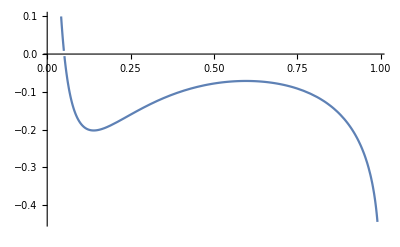

```mathematica
Plot[{fanalytic,%6},{u,0.01,0.99}]
```

```mathematica
NMaximize[{Abs[fanalytic-%6],u>0.0001,u<0.9999},u]
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of {Abs[11/24-ⅈ/π-(ⅈ π)/12-(29 u)/24+(3 ⅈ u)/π+(ⅈ π u)/6+(3 u^2)/4-(2 ⅈ u^2)/π-1/6 ⅈ π u^2+1/4 Log[-1+u]+«72»],u>0.0001,u<0.9999}.

Hold[NMaximize[{Abs[fanalytic-%6],u>0.0001,u<0.9999},u]]

```mathematica
data1 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,0.001,0.999, 0.001}];
```

```mathematica
data2 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,0.001,0.999, 0.0005}];
```

```mathematica
data3 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,1.1,5.1, 1}];
```

```mathematica
data4 = Table[{u,NIntegrate[f[p,u] ,{p,0,1}]},{u,-0.1,-1.1, -1}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.0917813}. NIntegrate obtained -2088.4-3483.46 ⅈ and 2184.44 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.525375}. NIntegrate obtained -53914.3+4921.65 ⅈ and 25060. for the integral and error estimates.

{{-0.1,-2088.4-3483.46 ⅈ},{-1.1,-53914.3+4921.65 ⅈ}}

```mathematica
points1000 = Sort[RandomReal[{0.001,0.999},1000]];
```

```mathematica
data5 = Map[{#,NIntegrate[f[p,#] ,{p,0,1}]}&,points1000];
```

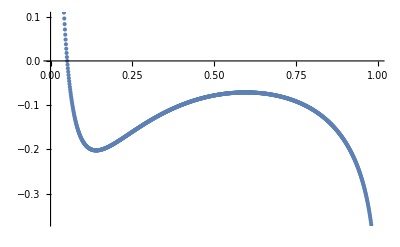

```mathematica
ListPlot[data1]
```

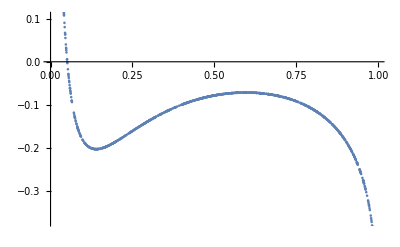

```mathematica
ListPlot[data5]
```

A union of uniform points and log uniform around 0 and 1

```mathematica
unipoints[nu_,nl_] :=  Sort[Join[Table[1/(nu*2^i),{i,2,nl+1}],
Table[1-1/(nu*2^i),{i,2,nl+1}],
RandomSample[Table[i/(16*nu),{i,1,16*nu-1}],nu]]]
```

```mathematica
unipoints70 = unipoints[50,10];
unipoints200 = unipoints[150,25];
```

```mathematica
residualdata2 = data2 - Table[{0,analytic },{u,0.001,0.999, 0.0005}];
```

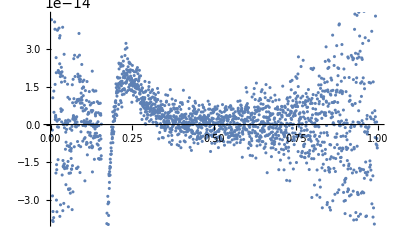

```mathematica
ListPlot[residualdata2]
```

```mathematica
data3 - Table[{0,analytic },{u,1.1,5.1,1}]
```

{{1.1,-1.34337×10^-14+0.989769 ⅈ},{2.1,1.10578×10^-13+1.90242 ⅈ},{3.1,-2.59348×10^-13-11.0846 ⅈ},{4.1,3.94351×10^-13-48.7715 ⅈ},{5.1,3.57758×10^-12-119.661 ⅈ}}

LinguisticAssistant

```mathematica
uvars = Variables[fanalytic]
```

{u,Log[-1+u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[2,u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)]}

```mathematica
vars = Prepend[Drop[uvars,1],1]
```

{1,Log[-1+u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[2,u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)]}

```mathematica
var2 = Flatten[Table[u^k1 Log[u]^k2 Log[1-u]^k3, {k1,0,2}, {k2,0,2},{k3,0,2}]]
```

{1,Log[1-u],Log[1-u]^2,Log[u],Log[1-u] Log[u],Log[1-u]^2 Log[u],Log[u]^2,Log[1-u] Log[u]^2,Log[1-u]^2 Log[u]^2,u,u Log[1-u],u Log[1-u]^2,u Log[u],u Log[1-u] Log[u],u Log[1-u]^2 Log[u],u Log[u]^2,u Log[1-u] Log[u]^2,u Log[1-u]^2 Log[u]^2,u^2,u^2 Log[1-u],u^2 Log[1-u]^2,u^2 Log[u],u^2 Log[1-u] Log[u],u^2 Log[1-u]^2 Log[u],u^2 Log[u]^2,u^2 Log[1-u] Log[u]^2,u^2 Log[1-u]^2 Log[u]^2}

```mathematica
allfns :=DeleteDuplicates[Flatten[Outer[Times,var2 ,vars]]];
```

```mathematica
fit1 := Fit[data1,allfns,u];
```

```mathematica
residual = fit1 - analytic;
```

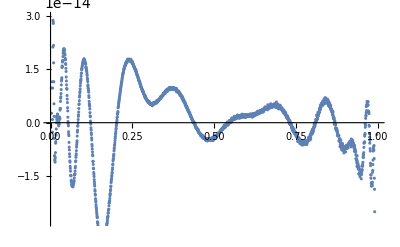

```mathematica
ListPlot[Table[{u,residual},{u,0.001,0.999,0.0005}]]
```

```mathematica
Table[residual,{u,1.1,5.1,1}]
```

{0.050324+0.841996 ⅈ,-1.22978+1.7403 ⅈ,-5.72846-8.19951 ⅈ,-14.1665-35.4037 ⅈ,-25.5688-83.6217 ⅈ}

```mathematica
fit2 := Fit[data2,allfns,u];
```

```mathematica
residual2 = fit2 - analytic;
```

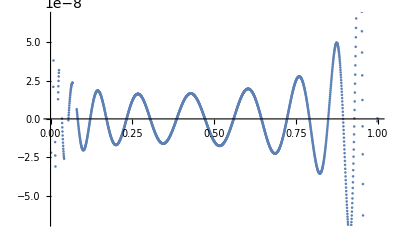

```mathematica
ListPlot[Table[{u,residual2},{u,0.001,0.999,0.0005}]]
```

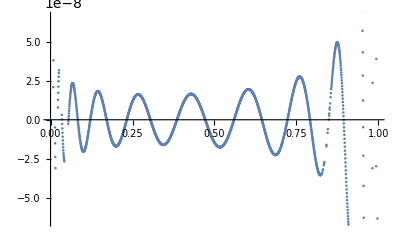

-Graphics-

```mathematica
Table[{u,residual},{u,0.001,0.999,0.05}]
```

{{0.001,2.18137×10^-11+2.02594×10^-15 ⅈ},{0.051,6.66134×10^-15-1.4615×10^-16 ⅈ},{0.101,1.7597×10^-14+3.42608×10^-16 ⅈ},{0.151,-3.28071×10^-14+5.84602×10^-16 ⅈ},{0.201,-8.60423×10^-16-1.13191×10^-16 ⅈ},{0.251,1.65423×10^-14-5.29524×10^-16 ⅈ},{0.301,5.71765×10^-15+2.30285×10^-16 ⅈ},{0.351,8.82627×10^-15+3.18322×10^-16 ⅈ},{0.401,7.23033×10^-15+8.75168×10^-16 ⅈ},{0.451,-2.30371×10^-15+3.33934×10^-16 ⅈ},{0.501,-3.95517×10^-15-2.04697×10^-16 ⅈ},{0.551,4.16334×10^-16-2.91434×10^-16 ⅈ},{0.601,1.81799×10^-15+3.31332×10^-16 ⅈ},{0.651,3.89966×10^-15+5.60316×10^-16 ⅈ},{0.701,4.48253×10^-15+1.37911×10^-16 ⅈ},{0.751,-3.78864×10^-15+2.09468×10^-16 ⅈ},{0.801,-2.02616×10^-15+5.37764×10^-17 ⅈ},{0.851,4.91274×10^-15+2.60209×10^-18 ⅈ},{0.901,-7.32747×10^-15+2.51535×10^-16 ⅈ},{0.951,-1.37668×10^-14+1.17961×10^-16 ⅈ}}

```mathematica
Table[{u,residual2},{u,0.001,0.999,0.05}]
```

{{0.001,3.36877×10^-9+3.7312×10^-10 ⅈ},{0.051,-1.2823×10^-8+1.43075×10^-10 ⅈ},{0.101,-2.03381×10^-8+7.73639×10^-11 ⅈ},{0.151,1.67929×10^-8-8.50378×10^-11 ⅈ},{0.201,-1.69166×10^-8+5.09317×10^-11 ⅈ},{0.251,1.23837×10^-8+9.09495×10^-13 ⅈ},{0.301,2.42289×10^-9-4.54747×10^-11 ⅈ},{0.351,-1.55487×10^-8+6.73026×10^-11 ⅈ},{0.401,8.92032×10^-9+3.27418×10^-11 ⅈ},{0.451,1.15142×10^-8-5.09317×10^-11 ⅈ},{0.501,-1.4923×10^-8+2.18279×10^-11 ⅈ},{0.551,-5.5079×10^-9+6.91216×10^-11 ⅈ},{0.601,1.95032×10^-8-2.18279×10^-11 ⅈ},{0.651,-5.18776×10^-9-1.09139×10^-11 ⅈ},{0.701,-1.84009×10^-8+6.18456×10^-11 ⅈ},{0.751,2.54659×10^-8-7.27596×10^-12 ⅈ},{0.801,-1.52431×10^-8-2.18279×10^-11 ⅈ},{0.851,6.59202×10^-9+5.82077×10^-11 ⅈ},{0.901,-3.49246×10^-8-4.36557×10^-11 ⅈ},{0.951,6.98128×10^-8-8.73115×10^-11 ⅈ}}

```mathematica
Table[{u,residual2},{u,1.1,5.1,1}]
```

{{1.1,207477.+350052. ⅈ},{2.1,4.55461×10^6-4.81679×10^6 ⅈ},{3.1,4.6817×10^6-3.45046×10^7 ⅈ},{4.1,-1.52265×10^7-1.06603×10^8 ⅈ},{5.1,-7.93256×10^7-2.37384×10^8 ⅈ}}

Now do the fit with the exact functions appearing in the analytic result.

```mathematica
FromCoefficientRules[Map[#[[1]] -> 1&,CoefficientRules[fanalytic ,uvars]],uvars] /. Plus->List
```

{1,u,u^2,{ⅈ π,Log[u]},{ⅈ π u,u Log[u]},{ⅈ π u^2,u^2 Log[u]},{-π^2,Log[u]^2},{-π^2 u,u Log[u]^2},{-π^2 u^2,u^2 Log[u]^2},{-ⅈ π^3,Log[u]^3},{-ⅈ π^3 u,u Log[u]^3},{-ⅈ π^3 u^2,u^2 Log[u]^3},Log[u],u Log[u],u^2 Log[u],{ⅈ π Log[u],Log[u]^2},{ⅈ π u Log[u],u Log[u]^2},{ⅈ π u^2 Log[u],u^2 Log[u]^2},{-π^2 Log[u],Log[u]^3},{-π^2 u Log[u],u Log[u]^3},{-π^2 u^2 Log[u],u^2 Log[u]^3},Log[u]^2,u Log[u]^2,u^2 Log[u]^2,{ⅈ π Log[u]^2,Log[u]^3},{ⅈ π u Log[u]^2,u Log[u]^3},{ⅈ π u^2 Log[u]^2,u^2 Log[u]^3},Log[u]^3,u Log[u]^3,u^2 Log[u]^3,{π^2/6,PolyLog[2,-u]},{(π^2 u)/6,u PolyLog[2,-u]},{PolyLog[2,-1/u],π^2/6},{u PolyLog[2,-1/u],(π^2 u)/6},{u^2 PolyLog[2,-1/u],(π^2 u^2)/6},{ⅈ π PolyLog[2,-1/u],1/6 π^2 Log[u]},{ⅈ π u PolyLog[2,-1/u],1/6 π^2 u Log[u]},{ⅈ π u^2 PolyLog[2,-1/u],1/6 π^2 u^2 Log[u]},{Log[u] PolyLog[2,-1/u],1/6 π^2 Log[u]},{u Log[u] PolyLog[2,-1/u],1/6 π^2 u Log[u]},{u^2 Log[u] PolyLog[2,-1/u],1/6 π^2 u^2 Log[u]},Log[u] PolyLog[2,u],u Log[u] PolyLog[2,u],u^2 Log[u] PolyLog[2,u],{PolyLog[3,-1/u],Zeta[3]},{u PolyLog[3,-1/u],u Zeta[3]},{u^2 PolyLog[3,-1/u],u^2 Zeta[3]},PolyLog[3,u],u PolyLog[3,u],u^2 PolyLog[3,u],{PolyLog[3,-u],Zeta[3]},{u PolyLog[3,-u],u Zeta[3]},{u^2 PolyLog[3,-u],u^2 Zeta[3]}}

```mathematica
newvars = Map[FromCoefficientRules[{#[[1]] -> 1},uvars]&,CoefficientRules[fanalytic ,uvars]]
```

{u^2 Log[-1+u]^3,u^2 Log[-1+u]^2 Log[u],u^2 Log[-1+u]^2,u^2 Log[-1+u] Log[u]^2,u^2 Log[-1+u] Log[u],u^2 Log[-1+u] PolyLog[2,(-1+u)/u],u^2 Log[-1+u],u^2 Log[u]^3,u^2 Log[u]^2,u^2 Log[u] PolyLog[2,(-1+u)/u],u^2 Log[u] PolyLog[2,u],u^2 Log[u],u^2 PolyLog[2,(-1+u)/u],u^2 PolyLog[3,(-1+u)/u],u^2 PolyLog[3,u],u^2 PolyLog[3,u/(-1+u)],u^2,u Log[-1+u]^3,u Log[-1+u]^2 Log[u],u Log[-1+u]^2,u Log[-1+u] Log[u]^2,u Log[-1+u] Log[u],u Log[-1+u] PolyLog[2,(-1+u)/u],u Log[-1+u],u Log[u]^3,u Log[u]^2,u Log[u] PolyLog[2,(-1+u)/u],u Log[u] PolyLog[2,u],u Log[u],u PolyLog[2,1-u],u PolyLog[2,(-1+u)/u],u PolyLog[3,(-1+u)/u],u PolyLog[3,u],u PolyLog[3,u/(-1+u)],u,Log[-1+u]^3,Log[-1+u]^2 Log[u],Log[-1+u]^2,Log[-1+u] Log[u]^2,Log[-1+u] Log[u],Log[-1+u] PolyLog[2,(-1+u)/u],Log[-1+u],Log[u]^3,Log[u]^2,Log[u] PolyLog[2,(-1+u)/u],Log[u] PolyLog[2,u],Log[u],PolyLog[2,1-u],PolyLog[2,(-1+u)/u],PolyLog[3,(-1+u)/u],PolyLog[3,u],PolyLog[3,u/(-1+u)],1}

```mathematica
newvars /. {Log[-1+u]->Log[1-u],PolyLog[n_,(-1+u)/u]->PolyLog[n,(-1+u)/u]
```

Can we make an orthogonal basis?

Find linear dependencies in this basis.

```mathematica
A = Map[newvars /. u->#&, points1000];
```

```mathematica
Dimensions[A]
```

{1000,53}

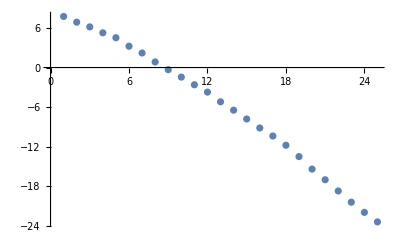

```mathematica
ListPlot[Log[SingularValueList[A]]]
```

```mathematica
Aext = Table[newvars,{u,-100.5,100.5}];
```

```mathematica
SingularValueList[Aext]
```

{1.70824×10^7,4.26625×10^6,140214.,35726.1,3163.74,1491.19,339.648,126.314,68.1923,37.1532,21.7691,15.5978,7.02936,2.88022,1.40406,0.431853,0.229878,0.0660124,0.0261652,0.00690755,0.00232937,0.000565835,0.000185965,0.0000353276,9.41528×10^-6,2.18758×10^-6,8.46934×10^-7}

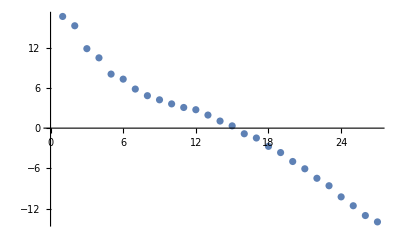

```mathematica
ListPlot[Log[SingularValueList[Aext]]]
```

```mathematica
Aextp60 = Table[N[newvars,60],{u,-100 - 1/2,100 + 1/2}];
```

```mathematica
Dimensions[Aextp60]
```

{202,53}

```mathematica
nullext = NullSpace[Aext];
```

```mathematica
N[newvars[[1]] /. u->100+1/2, 60]
```

983219.013206576757719645666045335733013314959817198097030167

```mathematica
n1000 = NullSpace[A];
```

```mathematica
n200 = NullSpace[ Map[newvars /. u->#&, Take[points1000,200]] ];
```

```mathematica
Dimensions[n1000]
```

{28,53}

```mathematica
nullvars = nullext . newvars;
```

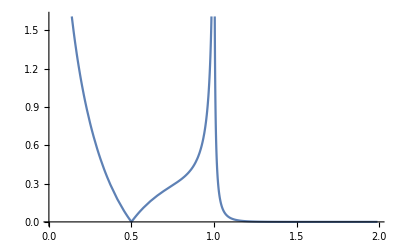

```mathematica
Plot[Abs[nullvars[[1]]],{u,0.01,1.99}]
```

```mathematica
newfit1 := Fit[data1,newvars,u];
```

```mathematica
newresidual = newfit1 - analytic;
```

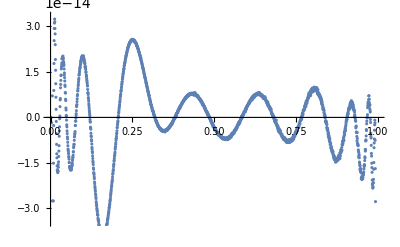

```mathematica
ListPlot[Table[{u,newresidual},{u,0.001,0.999,0.0005}]]
```

```mathematica
Table[newresidual,{u,1.1,5.1,1}]
```

{0.0047123+0.0160083 ⅈ,1.06618-0.203163 ⅈ,5.6863-7.88081 ⅈ,15.9849-31.0543 ⅈ,33.6937-76.1748 ⅈ}

```mathematica
newfit3 := Fit[Join[data5,data3],newvars,u];
```

```mathematica
newresidual3 = newfit3 - analytic;
```

```mathematica
Table[{u,newresidual3},{u,0.0005,0.999,0.01}]
```

{{0.0005,0.00174408+0.000136776 ⅈ},{0.0105,1.75023×10^-8+1.5616×10^-9 ⅈ},{0.0205,-1.50521×10^-8-1.29785×10^-9 ⅈ},{0.0305,9.11314×10^-10+1.31422×10^-9 ⅈ},{0.0405,6.94672×10^-9+4.1382×10^-11 ⅈ},{0.0505,-2.11912×10^-9-1.23509×10^-9 ⅈ},{0.0605,-7.44149×10^-9-8.44238×10^-10 ⅈ},{0.0705,-5.14592×10^-9+3.45608×10^-10 ⅈ},{0.0805,5.87534×10^-10+1.25192×10^-9 ⅈ},{0.0905,5.36238×10^-9+1.39653×10^-9 ⅈ},{0.1005,7.10315×10^-9+8.69932×10^-10 ⅈ},{0.1105,5.82531×10^-9+1.36424×10^-11 ⅈ},{0.1205,2.71029×10^-9-7.92625×10^-10 ⅈ},{0.1305,-8.56744×10^-10-1.31467×10^-9 ⅈ},{0.1405,-3.74439×10^-9-1.42836×10^-9 ⅈ},{0.1505,-5.31418×10^-9-1.16734×10^-9 ⅈ},{0.1605,-5.40149×10^-9-6.28461×10^-10 ⅈ},{0.1705,-4.17367×10^-9+5.00222×10^-11 ⅈ},{0.1805,-2.07638×10^-9+7.23958×10^-10 ⅈ},{0.1905,4.1382×10^-10+1.26784×10^-9 ⅈ},{0.2005,2.81852×10^-9+1.60799×10^-9 ⅈ},{0.2105,4.77939×10^-9+1.69939×10^-9 ⅈ},{0.2205,6.03177×10^-9+1.56524×10^-9 ⅈ},{0.2305,6.48015×10^-9+1.21236×10^-9 ⅈ},{0.2405,6.13272×10^-9+7.22139×10^-10 ⅈ},{0.2505,5.0959×10^-9+1.5325×10^-10 ⅈ},{0.2605,3.54885×10^-9-4.11546×10^-10 ⅈ},{0.2705,1.71985×10^-9-9.10859×10^-10 ⅈ},{0.2805,-1.75532×10^-10-1.29739×10^-9 ⅈ},{0.2905,-1.93268×10^-9-1.52386×10^-9 ⅈ},{0.3005,-3.36877×10^-9-1.57797×10^-9 ⅈ},{0.3105,-4.38558×10^-9-1.45155×10^-9 ⅈ},{0.3205,-4.90081×10^-9-1.16779×10^-9 ⅈ},{0.3305,-4.90991×10^-9-7.567×10^-10 ⅈ},{0.3405,-4.42333×10^-9-2.58296×10^-10 ⅈ},{0.3505,-3.54839×10^-9+2.81943×10^-10 ⅈ},{0.3605,-2.37287×10^-9+8.15817×10^-10 ⅈ},{0.3705,-1.01863×10^-9+1.28966×10^-9 ⅈ},{0.3805,3.78805×10^-10+1.67074×10^-9 ⅈ},{0.3905,1.6953×10^-9+1.92085×10^-9 ⅈ},{0.4005,2.82625×10^-9+2.02908×10^-9 ⅈ},{0.4105,3.67186×10^-9+1.97542×10^-9 ⅈ},{0.4205,4.1814×10^-9+1.77079×10^-9 ⅈ},{0.4305,4.30623×10^-9+1.427×10^-9 ⅈ},{0.4405,4.06158×10^-9+9.69521×10^-10 ⅈ},{0.4505,3.46654×10^-9+4.38376×10^-10 ⅈ},{0.4605,2.57887×10^-9-1.34605×10^-10 ⅈ},{0.4705,1.48657×10^-9-6.96673×10^-10 ⅈ},{0.4805,2.61934×10^-10-1.20235×10^-9 ⅈ},{0.4905,-9.6361×10^-10-1.62345×10^-9 ⅈ},{0.5005,-2.11412×10^-9-1.9154×10^-9 ⅈ},{0.5105,-3.08864×10^-9-2.05546×10^-9 ⅈ},{0.5205,-3.80851×10^-9-2.02454×10^-9 ⅈ},{0.5305,-4.20732×10^-9-1.8299×10^-9 ⅈ},{0.5405,-4.25507×10^-9-1.45974×10^-9 ⅈ},{0.5505,-3.93993×10^-9-9.56334×10^-10 ⅈ},{0.5605,-3.28032×10^-9-3.47427×10^-10 ⅈ},{0.5705,-2.32581×10^-9+3.28782×10^-10 ⅈ},{0.5805,-1.14801×10^-9+1.015×10^-9 ⅈ},{0.5905,1.59162×10^-10+1.66528×10^-9 ⅈ},{0.6005,1.49589×10^-9+2.21689×10^-9 ⅈ},{0.6105,2.74554×10^-9+2.6198×10^-9 ⅈ},{0.6205,3.80442×10^-9+2.83489×10^-9 ⅈ},{0.6305,4.56794×10^-9+2.83217×10^-9 ⅈ},{0.6405,4.95356×10^-9+2.59888×10^-9 ⅈ},{0.6505,4.91809×10^-9+2.13731×10^-9 ⅈ},{0.6605,4.44925×10^-9+1.47611×10^-9 ⅈ},{0.6705,3.55931×10^-9+6.49379×10^-10 ⅈ},{0.6805,2.30352×10^-9-2.64208×10^-10 ⅈ},{0.6905,7.98536×10^-10-1.1978×10^-9 ⅈ},{0.7005,-8.37872×10^-10-2.05728×10^-9 ⅈ},{0.7105,-2.44381×10^-9-2.75577×10^-9 ⅈ},{0.7205,-3.85717×10^-9-3.20415×10^-9 ⅈ},{0.7305,-4.909×10^-9-3.33876×10^-9 ⅈ},{0.7405,-5.47584×10^-9-3.1132×10^-9 ⅈ},{0.7505,-5.44856×10^-9-2.52385×10^-9 ⅈ},{0.7605,-4.79827×10^-9-1.6089×10^-9 ⅈ},{0.7705,-3.55521×10^-9-4.54747×10^-10 ⅈ},{0.7805,-1.8515×10^-9+8.06722×10^-10 ⅈ},{0.7905,1.21645×10^-10+2.00089×10^-9 ⅈ},{0.8005,2.08229×10^-9+2.92403×10^-9 ⅈ},{0.8105,3.71551×10^-9+3.40106×10^-9 ⅈ},{0.8205,4.71573×10^-9+3.25963×10^-9 ⅈ},{0.8305,4.82078×10^-9+2.43699×10^-9 ⅈ},{0.8405,3.89673×10^-9+9.82709×10^-10 ⅈ},{0.8505,2.0209×10^-9-9.04947×10^-10 ⅈ},{0.8605,-4.92491×10^-10-2.83217×10^-9 ⅈ},{0.8705,-3.07932×10^-9-4.26826×10^-9 ⅈ},{0.8805,-4.96357×10^-9-4.64433×10^-9 ⅈ},{0.8905,-5.35238×10^-9-3.50974×10^-9 ⅈ},{0.9005,-3.73598×10^-9-8.44921×10^-10 ⅈ},{0.9105,-3.04226×10^-10+2.67119×10^-9 ⅈ},{0.9205,3.6739×10^-9+5.41468×10^-9 ⅈ},{0.9305,5.79735×10^-9+5.18867×10^-9 ⅈ},{0.9405,3.5609×10^-9+5.69344×10^-10 ⅈ},{0.9505,-2.82012×10^-9-6.07542×10^-9 ⅈ},{0.9605,-6.56019×10^-9-5.86442×10^-9 ⅈ},{0.9705,2.32103×10^-9+8.14543×10^-9 ⅈ},{0.9805,4.51928×10^-9+2.18552×10^-9 ⅈ},{0.9905,7.05768×10^-10+6.85941×10^-9 ⅈ}}

```mathematica
Table[{u,newresidual3},{u,1.001,1.999,0.01}]
```

{{1.001,0.00351336-0.0204114 ⅈ},{1.011,-0.000989516+0.00804535 ⅈ},{1.021,0.00915336+0.0560016 ⅈ},{1.031,0.000989896+0.125359 ⅈ},{1.041,-0.0111043+0.203579 ⅈ},{1.051,-0.0188439+0.29308 ⅈ},{1.061,-0.0202411+0.398044 ⅈ},{1.071,-0.0164771+0.521401 ⅈ},{1.081,-0.0100076+0.664468 ⅈ},{1.091,-0.00358824+0.827231 ⅈ},{1.101,0.000192834+1.00872 ⅈ},{1.111,-0.00088205+1.20732 ⅈ},{1.121,-0.00859357+1.42103 ⅈ},{1.131,-0.024287+1.64764 ⅈ},{1.141,-0.048906+1.88486 ⅈ},{1.151,-0.0830405+2.13043 ⅈ},{1.161,-0.126977+2.38215 ⅈ},{1.171,-0.180749+2.63792 ⅈ},{1.181,-0.244179+2.89581 ⅈ},{1.191,-0.316926+3.15401 ⅈ},{1.201,-0.398512+3.41091 ⅈ},{1.211,-0.488359+3.66503 ⅈ},{1.221,-0.585812+3.91504 ⅈ},{1.231,-0.690162+4.15978 ⅈ},{1.241,-0.800666+4.39823 ⅈ},{1.251,-0.916556+4.62949 ⅈ},{1.261,-1.03706+4.8528 ⅈ},{1.271,-1.1614+5.06751 ⅈ},{1.281,-1.28883+5.27309 ⅈ},{1.291,-1.4186+5.46908 ⅈ},{1.301,-1.54999+5.65514 ⅈ},{1.311,-1.6823+5.831 ⅈ},{1.321,-1.81489+5.99646 ⅈ},{1.331,-1.94711+6.15139 ⅈ},{1.341,-2.07837+6.29571 ⅈ},{1.351,-2.20812+6.42943 ⅈ},{1.361,-2.33583+6.55256 ⅈ},{1.371,-2.46102+6.66518 ⅈ},{1.381,-2.58323+6.76741 ⅈ},{1.391,-2.70205+6.85939 ⅈ},{1.401,-2.8171+6.94129 ⅈ},{1.411,-2.92804+7.01333 ⅈ},{1.421,-3.03454+7.07571 ⅈ},{1.431,-3.13635+7.12868 ⅈ},{1.441,-3.23319+7.17249 ⅈ},{1.451,-3.32486+7.20742 ⅈ},{1.461,-3.41116+7.23374 ⅈ},{1.471,-3.49193+7.25174 ⅈ},{1.481,-3.56703+7.26171 ⅈ},{1.491,-3.63635+7.26395 ⅈ},{1.501,-3.6998+7.25877 ⅈ},{1.511,-3.7573+7.24646 ⅈ},{1.521,-3.80881+7.22733 ⅈ},{1.531,-3.85431+7.20167 ⅈ},{1.541,-3.89378+7.1698 ⅈ},{1.551,-3.92723+7.132 ⅈ},{1.561,-3.95468+7.08858 ⅈ},{1.571,-3.97617+7.03981 ⅈ},{1.581,-3.99176+6.98599 ⅈ},{1.591,-4.00151+6.92739 ⅈ},{1.601,-4.0055+6.86429 ⅈ},{1.611,-4.00381+6.79695 ⅈ},{1.621,-3.99654+6.72563 ⅈ},{1.631,-3.98381+6.65059 ⅈ},{1.641,-3.96572+6.57206 ⅈ},{1.651,-3.9424+6.49029 ⅈ},{1.661,-3.91398+6.40551 ⅈ},{1.671,-3.88059+6.31794 ⅈ},{1.681,-3.84239+6.2278 ⅈ},{1.691,-3.79951+6.13528 ⅈ},{1.701,-3.75211+6.0406 ⅈ},{1.711,-3.70034+5.94395 ⅈ},{1.721,-3.64437+5.8455 ⅈ},{1.731,-3.58434+5.74543 ⅈ},{1.741,-3.52044+5.64391 ⅈ},{1.751,-3.45281+5.54111 ⅈ},{1.761,-3.38164+5.43716 ⅈ},{1.771,-3.30708+5.33223 ⅈ},{1.781,-3.22931+5.22645 ⅈ},{1.791,-3.1485+5.11994 ⅈ},{1.801,-3.06481+5.01284 ⅈ},{1.811,-2.9784+4.90526 ⅈ},{1.821,-2.88946+4.79732 ⅈ},{1.831,-2.79815+4.6891 ⅈ},{1.841,-2.70463+4.58072 ⅈ},{1.851,-2.60906+4.47226 ⅈ},{1.861,-2.51162+4.36382 ⅈ},{1.871,-2.41246+4.25545 ⅈ},{1.881,-2.31173+4.14725 ⅈ},{1.891,-2.20961+4.03928 ⅈ},{1.901,-2.10624+3.9316 ⅈ},{1.911,-2.00177+3.82426 ⅈ},{1.921,-1.89635+3.71733 ⅈ},{1.931,-1.79014+3.61083 ⅈ},{1.941,-1.68327+3.50483 ⅈ},{1.951,-1.57588+3.39935 ⅈ},{1.961,-1.46813+3.29443 ⅈ},{1.971,-1.36013+3.19009 ⅈ},{1.981,-1.25203+3.08636 ⅈ},{1.991,-1.14394+2.98326 ⅈ}}

```mathematica
Log[-((-1+u) u)]//. {1-2u+2u^2 -> z1,Log[-((-1+u)u)]->z2}
```

z2

```mathematica
A = Map[newvars /. {Log[-1+u] -> Log[1-u]}/. u->#&, unipoints70];
```

```mathematica
Dimensions[A]
```

{70,53}

```mathematica
A100 = N[A,100];
```

```mathematica
A5 = RowReduce[A,Modulus->5];
```

RowReduce::nmod: {{-Log[102400/102399]^3/10485760000,-(Log[102400/102399]^2 Log[102400])/10485760000,Log[102400/102399]^2/10485760000,-(Log[102400/102399] Log[102400]^2)/10485760000,(Log[102400/102399] Log[102400])/10485760000,-(Log[102400/102399] PolyLog[2,-102399])/10485760000,-Log[102400/102399]/10485760000,-Log[102400]^3/10485760000,Log[102400]^2/10485760000,-(Log[102400] PolyLog[2,-102399])/10485760000,«43»},«9»,«60»} is not valid modulo 5.

```mathematica
A100rat = Rationalize[A100,0];
```

```mathematica
A100row = RowReduce[A100rat];
```

```mathematica
π
```

π